3D Rotational Matrix & NV orientations

```mathematica
(*Rotation matrices RzRyRz for B and B' *)
R[α_,β_,γ_] = {{Cos[α], -Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}}. {{Cos[β],0,Sin[β]},{0,1, 0},{-Sin[β],0,Cos[β]}} . {{Cos[γ], -Sin[γ],0},{Sin[γ],Cos[γ],0},{0,0,1}};
(*Refrence NV and magnetic field vector defined at 001*)
B = {0, 0, 50};
NV1 = {0,0,1}; 
NV2 = {2 √2,0,-1}/3; 
NV3 = {-√2,-√6,-1}/3; 
NV4 = {-√2,√6,-1}/3;
NV0={NV1,NV2,NV3,NV4};
(* these are the 4 orientations of our measured NVI in terms of rotation of our refrence NV0 for B and B' *)
(* apply the same rotation  *)
NVI1[α_,β_,γ_]=R[α,β,γ].NV0[[1]];
NVI2[α_,β_,γ_]=R[α,β,γ].NV0[[2]];
NVI3[α_,β_,γ_]=R[α,β,γ].NV0[[3]];
NVI4[α_,β_,γ_]=R[α,β,γ].NV0[[4]];
NVI= {NVI1,NVI2,NVI3,NVI4};
(* these are the angles between our measured NV and the magnetic field vector *)
ψ1[α_,β_,γ_]=ArcCos[NVI1[α,β,γ].B/Norm[B]];
ψ2[α_,β_,γ_]=ArcCos[NVI2[α,β,γ].B/Norm[B]];
ψ3[α_,β_,γ_]=ArcCos[NVI3[α,β,γ].B/Norm[B]];
ψ4[α_,β_,γ_]=ArcCos[NVI4[α,β,γ].B/Norm[B]];
ψ={ψ1,ψ2,ψ3,ψ4};
```

Peak frequencies (Hamiltonian solutions)

```mathematica
Clear[d,dd,γe,Dzfs,fn1,fn2,fn3,fn4,fp1,fp2,fp3,fp4,freqCostFunc,ddList, ddMean, ddMax, ddMin];
Clear[ddb,γe,Dzfsb,fn1b,fn2b,fn3b,fn4b,fp1b,fp2b,fp3b,fp4b,freqCostFuncb,ddListb, ddMeanb, ddMaxb, ddMinb];
γe=0.00280; (* electron gyromagnetic ratio in GHz/G *)
d = 2.87; (* zero-field splitting in GHz *)
Dzfs[dd_]=d+dd; (* Allowing for zero-field splitting shifts for B *)
Dzfsb[ddb_]=d+ddb; (* Allowing for zero-field splitting shifts for B' *)
(* these are the frequencies derived from the eigenvalues of the hamiltonian as a funtion of the rotation angles and the zfs shift for B *)
fp1[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ1[α,β,γ]])^2+γe*Norm[B]*Cos[ψ1[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ1[α,β,γ]])^2*(Sin[ψ1[α,β,γ]])^2);
fp2[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ2[α,β,γ]])^2+γe*Norm[B]*Cos[ψ2[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ2[α,β,γ]])^2*(Sin[ψ2[α,β,γ]])^2);
fp3[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ3[α,β,γ]])^2+γe*Norm[B]*Cos[ψ3[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ3[α,β,γ]])^2*(Sin[ψ3[α,β,γ]])^2);
fp4[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ4[α,β,γ]])^2+γe*Norm[B]*Cos[ψ4[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ4[α,β,γ]])^2*(Sin[ψ4[α,β,γ]])^2);

fn1[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ1[α,β,γ]])^2-γe*Norm[B]*Cos[ψ1[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ1[α,β,γ]])^2*(Sin[ψ1[α,β,γ]])^2);
fn2[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ2[α,β,γ]])^2-γe*Norm[B]*Cos[ψ2[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ2[α,β,γ]])^2*(Sin[ψ2[α,β,γ]])^2);
fn3[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ3[α,β,γ]])^2-γe*Norm[B]*Cos[ψ3[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ3[α,β,γ]])^2*(Sin[ψ3[α,β,γ]])^2);
fn4[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ4[α,β,γ]])^2-γe*Norm[B]*Cos[ψ4[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ4[α,β,γ]])^2*(Sin[ψ4[α,β,γ]])^2);
sModel[b_,c1_,c2_,c3_,c4_,df_,fn1_,fp1_,fn2_,fp2_,fn3_,fp3_,fn4_,fp4_,fdata_]=b-c1*(df^2/(4*(fdata-fp1)^2+df^2)+df^2/(4*(fdata-fn1)^2+df^2))-c2*(df^2/(4*(fdata-fp2)^2+df^2)+df^2/(4*(fdata-fn2)^2+df^2))-c3*(df^2/(4*(fdata-fp3)^2+df^2)+df^2/(4*(fdata-fn3)^2+df^2))-c4*(df^2/(4*(fdata-fp4)^2+df^2)+df^2/(4*(fdata-fn4)^2+df^2));
```

Generate ODMR Spectrum

```mathematica
myα = 0;
myβ = 0;
myγ = 0;
mydd = 0;
myfp1 = fp1[myα, myβ, myγ, mydd]
myfn1 = fn1[myα, myβ, myγ, mydd]
myfp2 = fp2[myα, myβ, myγ, mydd]
myfn2 = fn2[myα, myβ, myγ, mydd]
myfp3 = fp3[myα, myβ, myγ, mydd]
myfn3 = fn3[myα, myβ, myγ, mydd]
myfp4 = fp4[myα, myβ, myγ, mydd]
myfn4 = fn4[myα, myβ, myγ, mydd]
```

3.01

2.73

2.83234

2.92587

2.83234

2.92587

2.83234

2.92587

2.87

```mathematica
MWlowcut = 2.47;
MWhighcut = 3.27;
MWfreq = Range[MWlowcut, MWhighcut, 0.001];
MWfreqlen = Length[MWfreq];
ODMRSpectrum = ConstantArray[0, MWfreqlen];
For[i=1, i<=MWfreqlen, i++, ODMRSpectrum[[i]]=sModel[1, 0.05, 0.05,0.05,0.05,0.02,myfn1,myfp1,myfn2,myfp2,myfn3,myfp3,myfn4,myfp4,MWfreq[[i]]]];
plot=Transpose[{MWfreq, ODMRSpectrum}];
```

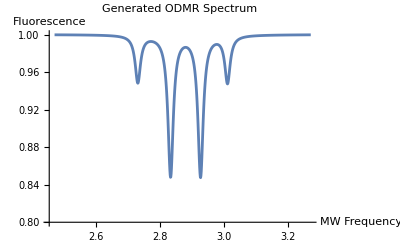

```mathematica
ListLinePlot[plot, PlotRange->{Automatic, {0.8, 1}},  AxesLabel->{"MW Frequency","Fluorescence"},PlotLabel->"Generated ODMR Spectrum"]
```

Fitting

```mathematica
(* Finding a fit while setting boundary conditions for B and B' *)
(* maximum possible shift: when magnetic field perfectly aligns *)
(* strains? can shift the center *)
dp=2.89;
dn=2.85;
fmin=(dn-(Norm[B]/10*28)/1000);
fmax=(dp+(Norm[B]/10*28)/1000);

fitResult =FindFit[plot,{sModel[b,c1,c2,c3,c4,df,fn1,fp1,fn2,fp2,fn3,fp3,fn4,fp4,fdata],{0.8<b<1.2,0<=c1<0.3,0<=c2<0.3,0<=c3<0.3,0<=c4<0.3,0.005<df<0.3,fmin<=fn1<dp,fmin<fn2<dp,fmin<fn3<dp,fmin<fn4<dp,dn<fp1<fmax,dn<fp2<fmax,dn<fp3<fmax,dn<fp4<fmax,(dn-0.02)<=(fn1+fp1)/2<=(dp+0.02),(dn-0.02)<=(fn2+fp2)/2<=(dp+0.02),(dn-0.02)<=(fn3+fp3)/2<=(dp+0.02),(dn-0.02)<=(fn4+fp4)/2<=(dp+0.02)}},{b,c1,c2,c3,c4,df,fp1,fn1,fn2,fp2,fn3,fp3,fn4,fp4},{fdata},MaxIterations->1000,Method->NMinimize];
```

```mathematica
fmin
```

2.71

```mathematica
fmax
```

3.03

```mathematica
fitResult
```

{b→1.,c1→0.05,c2→9.45753×10^-8,c3→0.15,c4→0.,df→0.02,fp1→3.01,fn1→2.73,fn2→2.84713,fp2→2.89,fn3→2.83234,fp3→2.92587,fn4→2.71241,fp4→3.0109}

Plot fitted result

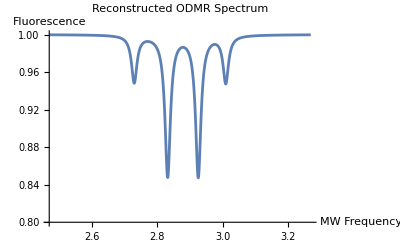

```mathematica
Plot[sModel[b,c1,c2,c3,c4,df,fn1,fp1,fn2,fp2,fn3,fp3,fn4,fp4,fdata]/.fitResult,{fdata,plot[[1]][[1]],plot[[-1]][[1]]},PlotPoints->1000,MaxRecursion->15,PlotRange->{Automatic, {0.8, 1}},  AxesLabel->{"MW Frequency","Fluorescence"},PlotLabel->"Reconstructed ODMR Spectrum"]
```

Resolve orientation from fitted frequencies

```mathematica
(* These are the fitted frequencies *)
freq ={fn1,fp1,fn2,fp2,fn3,fp3,fn4,fp4}/.fitResult[[7;;]]
freq = Sort[freq]
```

{2.73,3.01,2.84713,2.89,2.83234,2.92587,2.71241,3.0109}

{2.71241,2.73,2.83234,2.84713,2.89,2.92587,3.01,3.0109}

```mathematica
(* These are the true frequencies *)
myfreq={myfn1, myfp1, myfn2, myfp2, myfn3, myfp3, myfn4, myfp4}
myfreqSorted=Sort[myfreq]
```

{2.73,3.01,2.92587,2.83234,2.92587,2.83234,2.92587,2.83234}

{2.73,2.83234,2.83234,2.83234,2.92587,2.92587,2.92587,3.01}

```mathematica
freq=myfreqSorted;
freqCostFunc[α_,β_,γ_,dd_]=(fn1[α,β,γ,dd]-freq[[1]])^2+(fp1[α,β,γ,dd]-freq[[8]])^2+(fn2[α,β,γ,dd]-freq[[2]])^2+(fp2[α,β,γ,dd]-freq[[7]])^2+(fn3[α,β,γ,dd]-freq[[3]])^2+(fp3[α,β,γ,dd]-freq[[6]])^2+(fn4[α,β,γ,dd]-freq[[4]])^2+(fp4[α,β,γ,dd]-freq[[5]])^2;
ddMin=mydd -0.02;
ddMax=mydd+0.02;
eulerResult=NMinimize[{freqCostFunc[α,β,γ,dd],0<=α<=2π,0<=β<=2π,0<=γ<=2π,ddMin<dd<ddMax},{α,β,γ,dd}]
```

{0.0524878,{α→0.136777,β→6.28319,γ→0.116188,dd→4.83145×10^-6}}

```mathematica
freqCostFunc[α,β,γ,dd]/.eulerResult[[2]]
```

0.0524878

```mathematica
freqCostFunc[0, 0, 0, 0]
```

0.0524878

Plot Resolved NV orientations

```mathematica
v1=NVI1[α,β,γ]/.eulerResult[[2]][[1;;3]]
v2=NVI2[α,β,γ]/.eulerResult[[2]][[1;;3]]
v3=NVI3[α,β,γ]/.eulerResult[[2]][[1;;3]]
v4=NVI4[α,β,γ]/.eulerResult[[2]][[1;;3]]
```

{-8.99845×10^-8,-1.23851×10^-8,1.}

{0.912804,0.235962,-0.333333}

{-0.252053,-0.908492,-0.333333}

{-0.660751,0.67253,-0.333333}

```mathematica
Graphics3D[{Red,Arrow[{{0,0,0},NV1}],Purple,Arrow[{{0,0,0},NV2}],Purple,Arrow[{{0,0,0},NV3}],Purple,Arrow[{{0,0,0},NV4}]},PlotLabel->"True NV orientations"]
```

-Graphics3D-

```mathematica
Graphics3D[{Red,Arrow[{{0,0,0},v1}],Purple,Arrow[{{0,0,0},v2}],Purple,Arrow[{{0,0,0},v3}],Purple,Arrow[{{0,0,0},v4}]}, PlotLabel->"Reconstructed NV orientations"]
```

-Graphics3D-

Check if the Resolved frequencies give the input spectrum

```mathematica
resolvedfp1 = fp1[α,β,γ,dd]/.eulerResult[[2]];
resolvedfn1 = fn1[α,β,γ,dd]/.eulerResult[[2]];
resolvedfp2 = fp2[α,β,γ,dd]/.eulerResult[[2]];
resolvedfn2 = fn2[α,β,γ,dd]/.eulerResult[[2]];
resolvedfp3 = fp3[α,β,γ,dd]/.eulerResult[[2]];
resolvedfn3 = fn3[α,β,γ,dd]/.eulerResult[[2]];
resolvedfp4 = fp4[α,β,γ,dd]/.eulerResult[[2]];
resolvedfn4 = fn4[α,β,γ,dd]/.eulerResult[[2]];
```

```mathematica
resolvedfreq={resolvedfn1,resolvedfp1,resolvedfn2,resolvedfp2,resolvedfn3,resolvedfp3,resolvedfn4,resolvedfp4}
resolvedfreqSorted=Sort[resolvedfreq]
```

{2.78252,2.9561,2.79802,2.94299,2.93246,2.81014,2.96633,2.77009}

{2.77009,2.78252,2.79802,2.81014,2.93246,2.94299,2.9561,2.96633}

```mathematica
resolvedODMRSpectrum = ConstantArray[0, MWfreqlen];
For[i=1, i<=MWfreqlen, i++, resolvedODMRSpectrum[[i]]=sModel[1, 0.05, 0.05,0.05,0.05,0.02,resolvedfn1,resolvedfp1,resolvedfn2,resolvedfp2,resolvedfn3,resolvedfp3,resolvedfn4,resolvedfp4,MWfreq[[i]]]];
resolvedplot=Transpose[{MWfreq, resolvedODMRSpectrum}];
```

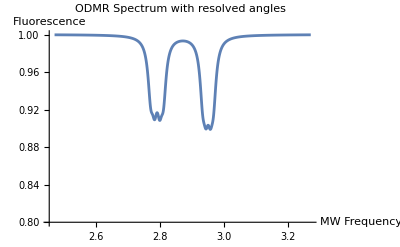

```mathematica
ListLinePlot[resolvedplot, PlotRange->{Automatic, {0.8, 1}},  AxesLabel->{"MW Frequency","Fluorescence"},PlotLabel->"ODMR Spectrum with resolved angles"]
```

```mathematica
2.87*1000- 2.8*50/2
```

2800.